## Two body kernel.

```mathematica
D[x/(√(y z)),x,y]//FullSimplify
```

-z/(2 (y z)^(3/2))

```mathematica
D[x/(√(y z)),{x,2}]//FullSimplify
```

0

## Calculate overlap of basis functions.

```mathematica
PhiN = Exp[(-(r-(rcut n)/nmax)^2)/(2 sig^2)]
```

ⅇ^(-(r-(n rcut)/nmax)^2/(2 sig^2))

```mathematica
PhiNPrime = Exp[(-(r-(rcut nprime)/nmax)^2)/(2 sig^2)]
```

ⅇ^(-(r-(nprime rcut)/nmax)^2/(2 sig^2))

```mathematica
SMat = Integrate[r^2*PhiN * PhiNPrime,{r,0,rcut}]//FullSimplify
```

1/(8 nmax^2)ⅇ^(-((n^2+nprime^2) rcut^2)/(2 nmax^2 sig^2)) sig (2 nmax (n+nprime-ⅇ^(((n-nmax+nprime) rcut^2)/(nmax sig^2)) (n+2 nmax+nprime)) rcut sig+ⅇ^(((n+nprime)^2 rcut^2)/(4 nmax^2 sig^2)) √π ((n+nprime)^2 rcut^2+2 nmax^2 sig^2) (Erf[((n+nprime) rcut)/(2 nmax sig)]-Erf[((n-2 nmax+nprime) rcut)/(2 nmax sig)]))

```mathematica
SMat/.{sig->0.5, nmax->14, n->4, nprime->6,rcut->5.0}
```

1.76315

## Calculate coefficient integral.

Write down and simplify the coefficient integral.

```mathematica
√(π/(4 α ri))Exp[-α ri^2] (2 α ri)^(l+1/2)/(2(α + βn))^(l+3/2)Exp[(α^2 ri^2)/(α + βn)]//FullSimplify
```

1/4 ⅇ^(-(ri^2 α βn)/(α+βn)) √π √(1/(ri α)) (ri α)^(1/2+l) (α+βn)^(-3/2-l)

Take the derivative with respect to neighbor distance.

```mathematica
D[1/4 ⅇ^(-(ri^2 α βn)/(α+βn)) √π √(1/(ri α)) (ri α)^(1/2+l) (α+βn)^(-3/2-l),ri]//FullSimplify
```

1/4 ⅇ^(-(ri^2 α βn)/(α+βn)) √π (1/(ri α))^(3/2) α (ri α)^(1/2+l) (α+βn)^(-5/2-l) (-2 ri^2 α βn+l (α+βn))

Compute double derivative with respect to alpha and neighbor distance, which will be needed for hyperparameter optimization.

```mathematica
D[1/4 ⅇ^(-(ri^2 α βn)/(α+βn)) √π (1/(ri α))^(3/2) α (ri α)^(1/2+l) (α+βn)^(-5/2-l) (-2 ri^2 α βn+l (α+βn)),α]//FullSimplify
```

1/8 ⅇ^(-(ri^2 α βn)/(α+βn)) √π √(1/(ri α)) (ri α)^(-1/2+l) (α+βn)^(-9/2-l) (2 l^2 βn (α+βn)^2-3 l α (α+βn) (α+βn+2 ri^2 βn^2)+2 ri^2 α βn (3 α^2+α βn+2 (-1+ri^2 α) βn^2))

Double check the double partial.

```mathematica
D[1/4 ⅇ^(-(ri^2 α βn)/(α+βn)) √π √(1/(ri α)) (ri α)^(1/2+l) (α+βn)^(-3/2-l),ri,α]//FullSimplify
```

1/8 ⅇ^(-(ri^2 α βn)/(α+βn)) √π √(1/(ri α)) (ri α)^(-1/2+l) (α+βn)^(-9/2-l) (2 l^2 βn (α+βn)^2-3 l α (α+βn) (α+βn+2 ri^2 βn^2)+2 ri^2 α βn (3 α^2+α βn+2 (-1+ri^2 α) βn^2))

## Check integral of product of 3D Gaussians.

```mathematica
Gauss1 = Exp[-((x-xi)^2+(y-yi)^2+(z-zi)^2)/(2 σ^2)]
```

ⅇ^((-(x-xi)^2-(y-yi)^2-(z-zi)^2)/(2 σ^2))

```mathematica
Gauss2 = Exp[-((x-xj)^2+(y-yj)^2+(z-zj)^2)/(2 σ^2)]
```

ⅇ^((-(x-xj)^2-(y-yj)^2-(z-zj)^2)/(2 σ^2))

```mathematica
Integrate[Gauss1 Gauss2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},Assumptions->{σ>0}]//FullSimplify
```

ⅇ^(-((xi-xj)^2+(yi-yj)^2+(zi-zj)^2)/(4 σ^2)) π^(3/2) σ^3

## Simplify power spectrum.

```mathematica
√((8 π^2)/(2l+1))16 π^2(2l+1)/(4 π)//FullSimplify
```

(8 π^2)/(√(1/(2+4 l)))

```mathematica
RiDotRj = (xi-x0)*(xj-x0)+(yi-y0)*(yj-y0)+(zi-z0)*(zj-z0)
```

(-x0+xi) (-x0+xj)+(-y0+yi) (-y0+yj)+(-z0+zi) (-z0+zj)

```mathematica
Ri = √((xi-x0)^2+(yi-y0)^2+(zi-z0)^2)
```

√((-x0+xi)^2+(-y0+yi)^2+(-z0+zi)^2)

```mathematica
Rj=√((xj-x0)^2+(yj-y0)^2+(zj-z0)^2)
```

√((-x0+xj)^2+(-y0+yj)^2+(-z0+zj)^2)

```mathematica
D[RiDotRj/(Ri Rj),x0]/.{x0->0,y0->0,z0->0}//FullSimplify
```

(xj (xi^2+yi^2+zi^2) (xi xj+yi yj+zi zj)-(xi+xj) (xi^2+yi^2+zi^2) (xj^2+yj^2+zj^2)+xi (xi xj+yi yj+zi zj) (xj^2+yj^2+zj^2))/((xi^2+yi^2+zi^2)^(3/2) (xj^2+yj^2+zj^2)^(3/2))

## Calculate overlap of Gaussian basis functions.

```mathematica
Phinl = r^l Exp[-βn r^2]
PhinlPrime = r^l Exp[-βnprime r^2]
```

ⅇ^(-r^2 βn) r^l

ⅇ^(-r^2 βnprime) r^l

```mathematica
SMat = Integrate[r^2*Phinl * PhinlPrime,{r,0,Infinity},Assumptions->{l>0,βn>0,βnprime>0}]//FullSimplify
```

1/2 (βn+βnprime)^(-3/2-l) Gamma[3/2+l]

```mathematica
N[Gamma[4.5]]
```

11.6317

## Calculate overlap between Gaussian and basis function.

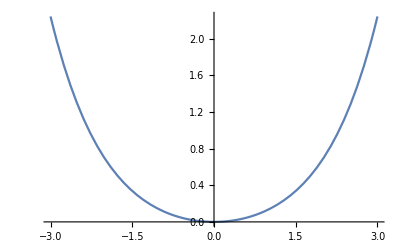

```mathematica
Plot[BesselI[2,x],{x,-3,3}]
```

```mathematica
CFunc = Exp[-alpha (r^2+ri^2)]Exp[-alpha (r^2+rj^2)]BesselI[l,2*alpha*r*ri]//FullSimplify
```

ⅇ^(-alpha (2 r^2+ri^2+rj^2)) BesselI[l,2 alpha r ri]

```mathematica
Integrate[CFunc,{r,0,Infinity}, Assumptions->{r>0,ri>0,rb>0,alpha>0,l>0}]
```

(ⅇ^(-alpha ((3 ri^2)/4+rj^2)) √(π/2) BesselI[l/2,(alpha ri^2)/4])/(2 √alpha)

```mathematica
AtomOverlap =(1/r) Exp[-a r^2]BesselI[l,b r]BesselI[l,c r]//FullSimplify
```

(ⅇ^(-a r^2) BesselI[l,b r] BesselI[l,c r])/r

```mathematica
Integrate[AtomOverlap,{r,0,Infinity}]
```

∫_0^∞ (ⅇ^(-a r^2) BesselI[l,b r] BesselI[l,c r])/r ⅆr

```mathematica
SphFunc = Exp[-alpha (r^2+ri^2)]Exp[-alpha (r-rj)]BesselI[l,2*alpha*r*ri]//FullSimplify
```

```mathematica
Integrate[BesselI[nu, b*t]*Exp[-p^2 (t-a)^2],{t,0,Infinity}]
```

∫_0^∞ ⅇ^(-p^2 (-a+t)^2) BesselI[nu,b t]ⅆt

```mathematica
Integrate[t^(nu+1) BesselI[nu, b*t]*Exp[-p^2 t^2],{t,0,Infinity}]
```

ConditionalExpression[2^(-1-nu) b^nu ⅇ^(b^2/(4 p^2)) (p^2)^(-1-nu),Re[b]≥0&&(Im[b]>0||Re[b]>0)&&Re[nu]>-1&&Re[p^2]>0]

```mathematica
Integrate[t^(nu+1) BesselI[nu, b*t]*Exp[-p^2 t^2],{t,0,Infinity}]
```

ConditionalExpression[2^(-1-nu) (b^2)^(nu/2) ⅇ^(b^2/(4 p^2)) (p^2)^(-1-nu),Re[nu]>-1]

```mathematica
Integrate[t^nu BesselI[nu, b*t]*Exp[-p^2 t^2],{t,0,Infinity}]
```

ConditionalExpression[2^(-1-nu) b^nu (p^2)^(-1/2-nu) Gamma[1/2+nu] Hypergeometric1F1Regularized[1/2+nu,1+nu,b^2/(4 p^2)],Re[b]≥0&&1+2 Re[nu]>0&&Re[p^2]≥0&&(2 Re[nu]<1||Re[p^2]≠0)&&(Re[b]>0||Im[b]>0)]

## Scrap.

```mathematica
D[x^n,x]
```

n x^(-1+n)